```mathematica
Needs["ErrorBarPlots`"]
SetOptions[{ListDensityPlot,ListPlot,Plot},BaseStyle->{FontFamily->"CMU Serif",FontSize->12},FrameStyle->Directive[Black,Thickness[.001]]];

data=Import["C:/Users/Ian/Desktop/gravlensingproject/data.csv"];
theta=data⟦;;,1⟧;
ellipticity=data⟦;;,2⟧;
σellipticity=data⟦;;,3⟧;
```

```mathematica
H0=69.32 Quantity[, ("Kilometers")/("Megaparsecs" "Seconds")];
ρcrit=UnitConvert[(3 H0^2)/(8π Quantity[, "GravitationalConstant"]),"SI"];
DL=1 Quantity[, "Gigaparsecs"];
DS=3 Quantity[, "Gigaparsecs"];
criticalSurfaceDensity=UnitConvert[Quantity[, "SpeedOfLight"]^2/(4π Quantity[, "GravitationalConstant"])*DS/((DS-DL)*DL),"SI"];
```

## NFW Fit

```mathematica
rs=UnitConvert[M200^(1/3)/c((3(Quantity[, "SolarMass"]))/(800π ρcrit))^(1/3),"SI"];
θs=rs/DL*QuantityMagnitude[Quantity[, "Radians"],Quantity[, "ArcSeconds"]];
δc=200/3*c^3/(Log[1+c]-c/(1+c));
```

```mathematica
NFWsurfaceDensity=(2δc*ρcrit*rs)/((θ/θs)^2-1)(1-2/(√((θ/θs)^2-1))ArcTan[√((θ/θs-1)/(θ/θs+1))]) ;
NFWaverageSurfaceDensity=(4δc*ρcrit*rs)/(θ/θs)^2(2/(√((θ/θs)^2-1))ArcTan[√((θ/θs-1)/(θ/θs+1))]+Log[(θ/θs)/2]) ;
NFWconvergence=NFWsurfaceDensity/criticalSurfaceDensity;
NFWshear=Simplify[Expand[(NFWaverageSurfaceDensity-NFWsurfaceDensity)/criticalSurfaceDensity]];
NFWreducedShear=NFWshear/(1-NFWconvergence);
NFWellipticity=(2*NFWreducedShear)/(1+NFWreducedShear^2);
```

```mathematica
NFWchiSquared=Total[((ellipticity-Re[(NFWellipticity/.θ->theta)])/σellipticity)^2];
NFWfit=NMinimize[{NFWchiSquared/.M200->10^logM200,10<logM200<20,0<c<50},{logM200,c},PrecisionGoal->10,WorkingPrecision->10]
```

{53.25597593,{logM200→14.98298964,c→10.24874817}}

```mathematica
logM200RangeNFW={14.8,15.2};
cRange={5,20};
resolutionNFW=100;
NFWchiSquaredTable=Flatten[Table[{logM200,c,NFWchiSquared/.M200->10^logM200},
{logM200,logM200RangeNFW⟦1⟧,logM200RangeNFW⟦2⟧,(logM200RangeNFW⟦2⟧-logM200RangeNFW⟦1⟧)/resolutionNFW},
{c,cRange⟦1⟧,cRange⟦2⟧,(cRange⟦2⟧-cRange⟦1⟧)/resolutionNFW}],1];
```

```mathematica
Pc=1/(cRange⟦2⟧-cRange⟦1⟧);
PlogM200NFW=1/(logM200RangeNFW⟦2⟧-logM200RangeNFW⟦1⟧);
cellSizeNFW=(logM200RangeNFW⟦2⟧-logM200RangeNFW⟦1⟧)/resolutionNFW*(cRange⟦2⟧-cRange⟦1⟧)/resolutionNFW;
PNFW=Transpose[{NFWchiSquaredTable⟦;;,1⟧,NFWchiSquaredTable⟦;;,2⟧,ⅇ^(-NFWchiSquaredTable⟦;;,3⟧/2)*Pc*PlogM200NFW}];
NFWprobabilityNormalization=1/Total[PNFW⟦;;,3⟧*cellSizeNFW];
PNFWNormalized=Transpose[{PNFW⟦;;,1⟧,PNFW⟦;;,2⟧,NFWprobabilityNormalization*PNFW⟦;;,3⟧}];
integratedProbabilityNFW[lowerCut_]:=Total[Clip[PNFWNormalized⟦;;,3⟧,{lowerCut,∞},{0,∞}]*cellSizeNFW]
findProbabilityContourNFW[p_]:=Block[{pc=0},While[integratedProbabilityNFW[pc]-p>0.001,pc=pc+.001];pc]
```

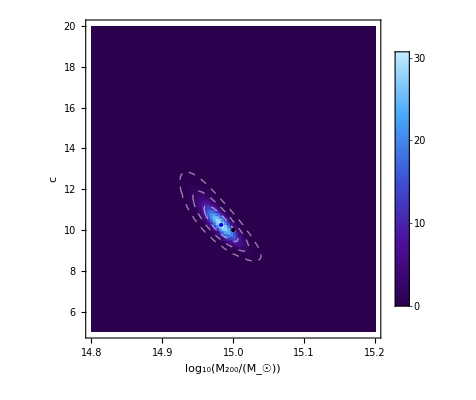

```mathematica
Show[
ListDensityPlot[PNFWNormalized,PlotRange->All,ColorFunction->"DeepSeaColors",PlotLegends->Automatic,InterpolationOrder->5],
ListContourPlot[PNFWNormalized,PlotRange->All,
Contours->Table[findProbabilityContourNFW[p],{p,{0.68,0.95,0.997}}],
ContourShading->None,ContourStyle->{{White,Dashed}}],
Graphics[{Blue,Point[{logM200,c}/.NFWfit⟦2⟧],Black,Point[{15,10}]}],
FrameLabel->{"log_10(M_200/(M_☉))","c"}]
```

## Isothermal Fit

```mathematica
r200=UnitConvert[M200^(1/3)((3 Quantity[, "SolarMass"])/(800π ρcrit))^(1/3),"SI"];
σ2=(M200 Quantity[, "SolarMass"]Quantity[, "GravitationalConstant"] /Quantity[, "Meters"])/Expand[2(r200-DL θc ArcTan[r200/(DL θc)])*1/Quantity[, "Meters"]];
```

```mathematica
ISOsurfaceDensity=σ2/(2 Quantity[, "GravitationalConstant"]DL √(θ^2+θc^2)) ;
ISOaverageSurfaceDensity=(σ2(√(θ^2+θc^2)-θc))/(2 Quantity[, "GravitationalConstant"]DL θ^2) ;
ISOconvergence=ISOsurfaceDensity/criticalSurfaceDensity;
ISOshear=Simplify[Expand[(ISOaverageSurfaceDensity-ISOsurfaceDensity)/criticalSurfaceDensity]];
ISOreducedShear=ISOshear/(1-ISOconvergence);
ISOellipticity=(2*ISOreducedShear)/(1+ISOreducedShear^2)/.{θ->t*QuantityMagnitude[Quantity[, "ArcSeconds"],Quantity[, "Radians"]],θc->tc*QuantityMagnitude[Quantity[, "ArcSeconds"],Quantity[, "Radians"]]};
```

```mathematica
ISOchiSquared=Total[((ellipticity+(ISOellipticity/.t->theta))/σellipticity)^2];
ISOfit=NMinimize[{ISOchiSquared/.M200->10^logM200,10<logM200<20,0<tc<1000},{logM200,tc},PrecisionGoal->10,WorkingPrecision->10]
```

{218.0280594,{logM200→15.84506667,tc→90.57757587}}

```mathematica
logM200RangeISO={15.7,16.0};
tcRange={80,120};
resolutionISO=100;
ISOchiSquaredTable=Flatten[Table[{logM200,tc,ISOchiSquared/.M200->10^logM200},
{logM200,logM200RangeISO⟦1⟧,logM200RangeISO⟦2⟧,(logM200RangeISO⟦2⟧-logM200RangeISO⟦1⟧)/resolutionISO},
{tc,tcRange⟦1⟧,tcRange⟦2⟧,(tcRange⟦2⟧-tcRange⟦1⟧)/resolutionISO}],1];
```

```mathematica
PlogM200ISO=1/(logM200RangeISO⟦2⟧-logM200RangeISO⟦1⟧);
Ptc=1/(tcRange⟦2⟧-tcRange⟦1⟧);
cellSizeISO=(logM200RangeISO⟦2⟧-logM200RangeISO⟦1⟧)/resolutionISO*(tcRange⟦2⟧-tcRange⟦1⟧)/resolutionISO;
PISO=Transpose[{ISOchiSquaredTable⟦;;,1⟧,ISOchiSquaredTable⟦;;,2⟧,ⅇ^(-ISOchiSquaredTable⟦;;,3⟧/2)*Ptc*PlogM200ISO}];
ISOprobabilityNormalization=1/Total[PISO⟦;;,3⟧*cellSizeISO];
PISONormalized=Transpose[{PISO⟦;;,1⟧,PISO⟦;;,2⟧,ISOprobabilityNormalization*PISO⟦;;,3⟧}];
integratedProbabilityISO[lowerCut_]:=Total[Clip[PISONormalized⟦;;,3⟧,{lowerCut,∞},{0,∞}]*cellSizeISO]
findProbabilityContourISO[p_]:=Block[{pc=0},While[integratedProbabilityISO[pc]-p>0.001,pc=pc+.001];pc]
```

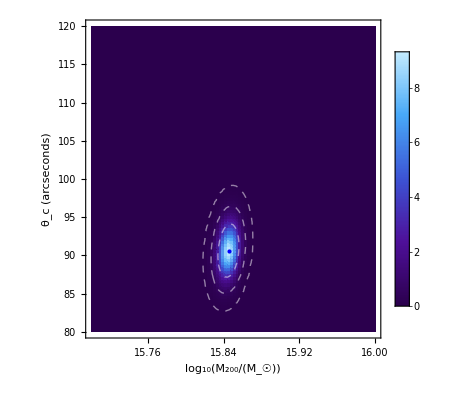

```mathematica
Show[
ListDensityPlot[PISONormalized,PlotRange->All,ColorFunction->"DeepSeaColors",PlotLegends->Automatic],
ListContourPlot[PISONormalized,PlotRange->All,
Contours->Table[findProbabilityContourISO[p],{p,{0.68,0.95,0.997}}],
ContourShading->None,ContourStyle->{{White,Dashed}}],
Graphics[{Blue,Point[{logM200,tc}/.ISOfit⟦2⟧]}],
FrameLabel->{"log_10(M_200/(M_☉))","θ_c (arcseconds)"}
]
```

## Comparison

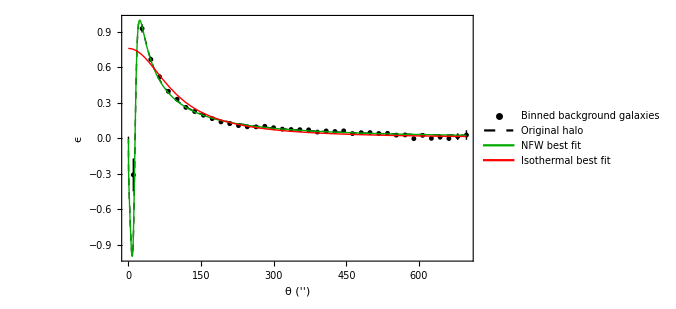

```mathematica
Show[
ErrorListPlot[Transpose[{Transpose[{theta,ellipticity}],ErrorBar/@σellipticity}],PlotRange->{{0,All},{0,All}},PlotStyle->{Black,PointSize[0.007],Thickness[0.002]},PlotLegends->Placed[LineLegend[{Black,{Black,Dashed},Darker[Green],Red},
{"Binned background galaxies","Original halo","NFW best fit","Isothermal best fit"},LabelStyle->{FontFamily->"CMU Serif",FontSize->12},Joined->{False,True,True,True},LegendMarkerSize->{{10,7},{15,5},{15,5},{15,5}}],{.8,.8}]],
Plot[NFWellipticity/.{M200->10^15,c->10},{θ,.0,Max[theta]},
PlotRange->All,PlotLegends->{},PlotStyle->{Dashed,Black,Thickness[0.002]}],
Plot[(NFWellipticity/.M200->10^logM200)/.NFWfit⟦2⟧,{θ,0,Max[theta]},
PlotRange->All,PlotLegends->{},PlotStyle->{Darker[Green],Thickness[0.002]}],
Plot[(-ISOellipticity/.M200->10^logM200)/.ISOfit⟦2⟧,{t,0,Max[theta]},
PlotRange->All,PlotLegends->{},PlotStyle->{Red,Thickness[0.002]}],
PlotRange->{0,All},Frame->True,FrameLabel->{"θ ('')","ϵ"},ImageSize->500
]
```

```mathematica
PNFWintegrated=Total[PNFW⟦;;,3⟧*cellSizeNFW];
PISOintegrated=Total[PISO⟦;;,3⟧*cellSizeISO];
evidenceRatio=PNFWintegrated/PISOintegrated
```

3.67292×10^35